```mathematica
ClearAll["Global`*"];
Lmin = 0;
Lmax = +1;
Vmin = -10;
Vmax = +10;
nx = 1;
kx = 2 Pi/((Lmax - Lmin)/nx);
nv = 2;
kv =  2 Pi/((Vmax - Vmin)/nv);
w =1;
LevX=4;
LevV=4;
Deg=3;
dt=N[Lmax/(2^LevX)/Vmax(2*Deg+1)]
nt=100;
fx:= Sin[kx x ];
ft:= Sin[w t];
fv:= Sin[kv v];
f:=fx fv ft;
Ex:=Cos[kx x];
Et:=Cos[w t];
EE:=Ex Et;
f
fx[Lmin]
0.04375
Sin[t] Sin[(π v)/5] Sin[2 π x]
Sin[2 π x][0]
```

0.04375

Sin[t] Sin[(π v)/5] Sin[2 π x]

Sin[2 π x][0]

0.04375

Sin[t] Sin[(π v)/5] Sin[2 π x]

Sin[2 π x][0]

```mathematica
source1=D[f,t]
source2=v D[f,x]
source3 = EE D[f,v]
dt*nt
```

Cos[t] Sin[(π v)/5] Sin[2 π x]

2 π v Cos[2 π x] Sin[t] Sin[(π v)/5]

1/5 π Cos[t] Cos[(π v)/5] Cos[2 π x] Sin[t] Sin[2 π x]

4.375

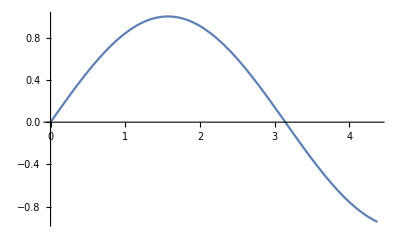

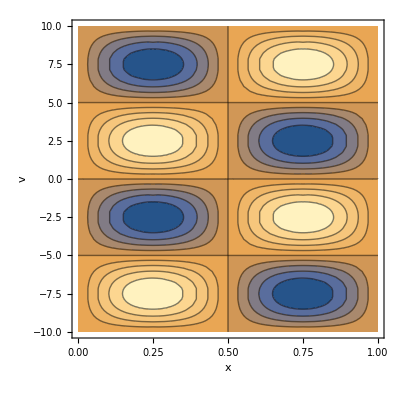

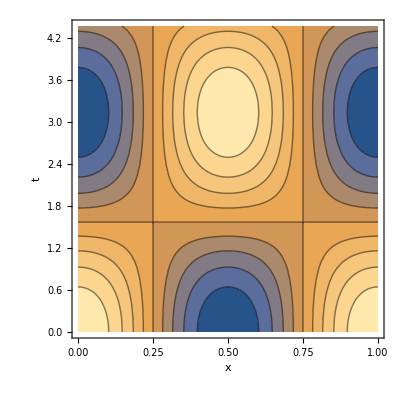

```mathematica
Plot[ft,{t,0,nt dt}]
t=0.1;
ContourPlot[f,{x,Lmin,Lmax},{v,Vmin,Vmax},FrameLabel->Automatic]
ContourPlot[EE,{x,Lmin,Lmax},{t,0,nt dt},FrameLabel->Automatic]
```

## continuity1 test case (1D)

```mathematica
ClearAll["Global`*"];
D[f[x,t],t]+v D[f[x,t],x]==0 // Defer // TraditionalForm
```

v (∂f(x,t))/(∂x)+(∂f(x,t))/(∂t)==0

```mathematica
xMin=-1;
xMax=+1;
ft=Sin[w t]; 
fx=Cos[k x];
w=1;
n=2;
v=1;
k=2 Pi/((xMax-xMin)/n);
f=ft fx;
source1=D[f,t]
source2=v D[f,x]
```

Cos[t] Cos[2 π x]

-2 π Sin[t] Sin[2 π x]

```mathematica
-2 π Sin[t] Sin[2 π x]
```

## continuity2 test case (2D)

```mathematica
ClearAll["Global`*"];
D[f[x,y,t],t]+Subscript[v, x] D[f[x,y,t],x]+Subscript[v, y] D[f[x,y,t],y]==0 // Defer // TraditionalForm
```

v_x (∂f(x,y,t))/(∂x)+v_y (∂f(x,y,t))/(∂y)+(∂f(x,y,t))/(∂t)==0

```mathematica
xMin=-1;
xMax=+1;
yMin=-2;
yMax=+2;
ft=Sin[w t];
fx=Cos[kx x];
fy=Sin[ky y];
w=2;
nx=1;
ny=4;
vx=1;
vy=1;
kx=2 Pi/((xMax-xMin)/nx);
ky=2 Pi/((yMax-yMin)/ny);
v={vx,vy};
f=fx fy ft;
StringForm["Analytic solution: f(x,y,t)=``",f]
source1=D[f,t];
source2=v.Grad[f,{x,y}];
StringForm["Source 1: ``",source1]
StringForm["Source 2: ``",source2[[1]]]
StringForm["Source 3: ``",source2[[2]]]
t=0;
StringForm["Initial condition: f(x,y,z,t)=``",f]
```

Analytic solution: f(x,y,t)=Cos[π x] Sin[2 t] Sin[2 π y]

Source 1: 2 Cos[2 t] Cos[π x] Sin[2 π y]

Source 2: 2 π Cos[π x] Cos[2 π y] Sin[2 t]

Source 3: -π Sin[2 t] Sin[π x] Sin[2 π y]

Initial condition: f(x,y,z,t)=0

## continuity3 test case (3D)

```mathematica
ClearAll["Global`*"];
D[f[x,y,z,t],t]+Subscript[v, x] D[f[x,y,z,t],x]+Subscript[v, y] D[f[x,y,z,t],y]+Subscript[v, z] D[f[x,y,z,t],z]==0 // Defer // TraditionalForm
xMin=-1;
xMax=+1;
yMin=-2;
yMax=+2;
zMin=-3;
zMax=+3;
ft=Sin[w t];
fx=Cos[kx x];
fy=Sin[ky y];
fz=Cos[kz z];
w=2;
nx=1;
ny=4;
nz=2;
vx=1;
vy=1;
vz=3;
kx=2 Pi/((xMax-xMin)/nx);
ky=2 Pi/((yMax-yMin)/ny);
kz=2 Pi/((zMax-zMin)/nz);
v={vx,vy,vz};
f=fx fy fz ft;
StringForm["Analytic solution: f(x,y,z,t)=``",f]
source1=D[f,t];
source2=v.Grad[f,{x,y,z}];
StringForm["Source 1: ``",source1]
StringForm["Source 2: ``",source2[[1]]]
StringForm["Source 3: ``",source2[[2]]]
StringForm["Source 4: ``",source2[[3]]]
t=0;
StringForm["Initial condition: f(x,y,z,t)=``",f]
```

v_x (∂f(x,y,z,t))/(∂x)+v_y (∂f(x,y,z,t))/(∂y)+v_z (∂f(x,y,z,t))/(∂z)+(∂f(x,y,z,t))/(∂t)==0

Analytic solution: f(x,y,z,t)=Cos[π x] Cos[(2 π z)/3] Sin[2 t] Sin[2 π y]

Source 1: 2 Cos[2 t] Cos[π x] Cos[(2 π z)/3] Sin[2 π y]

Source 2: 2 π Cos[π x] Cos[2 π y] Cos[(2 π z)/3] Sin[2 t]

Source 3: -π Cos[(2 π z)/3] Sin[2 t] Sin[π x] Sin[2 π y]

Source 4: -2 π Cos[π x] Sin[2 t] Sin[2 π y] Sin[(2 π z)/3]

Initial condition: f(x,y,z,t)=0